```mathematica
data = ReadList["./week1proj/output.log", {Number, Number}]
```

{{0.,-17.78},{5.,-15.},{10.,-12.22},{15.,-9.44},{20.,-6.67},{25.,-3.89},{30.,-1.11},{35.,1.67},{40.,4.44},{45.,7.22},{50.,10.},{55.,12.78},{60.,15.56},{65.,18.33},{70.,21.11},{75.,23.89},{80.,26.67},{85.,29.44},{90.,32.22},{95.,35.},{100.,37.78}}

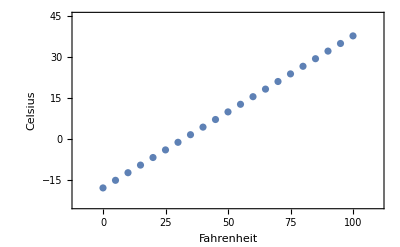

```mathematica
g = ListPlot[data,Frame->True,PlotRange->{{-10,110},{-24,45}},FrameLabel->{"Fahrenheit","Celsius"}]
```

```mathematica
Export["./week1proj/fig.pdf",g]
```

./week1proj/fig.pdf

```mathematica
Directory[]
```

C:\Users\Caden Gobat\Documents\GitHub\PHYS-3181